# P-Value Hacking

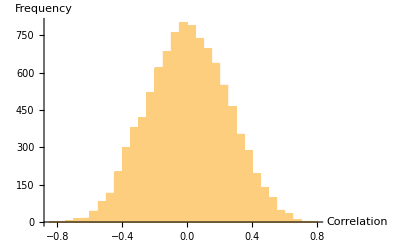

```mathematica
Histogram[Table[a = RandomVariate[NormalDistribution[],18];
b = RandomVariate[NormalDistribution[],18]; Correlation[a,b],{10000}], AxesLabel->{"Correlation","Frequency"}]
```

```mathematica
dist1=NormalDistribution[0.3,1];
ta = Table[ran=RandomVariate[dist1,20];
SurvivalFunction[StudentTDistribution[20], Mean[ran]/(StandardDeviation[ran]/Sqrt[20])],{10^4}];
```

```mathematica
Mean[ta] (*Most options are below the p-value 0.05*)
```

0.175591

```mathematica
?Quantile
```

```mathematica
Quantile[ta,0.36590] // N
```

0.0499641

```mathematica
Quantile[ta,0.025] // N
```

0.000794859

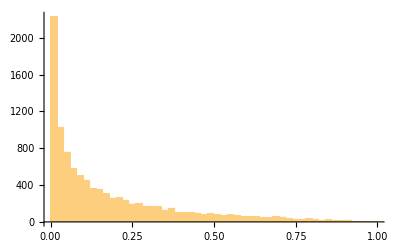

```mathematica
Histogram[ta,60]
```

```mathematica
CDF[EmpiricalDistribution[ta], 0.01]
```

0.1457